```mathematica
g=9.8;
data=Table[1/2 g  i^2,{i,1,10}]
```

{4.9,19.6,44.1,78.4,122.5,176.4,240.1,313.6,396.9,490.}

```mathematica
data = Table[1/2 g i^2(1+0.2 RandomReal[]),{i,1,10}]
```

{5.61799,21.5002,44.8836,83.918,138.765,180.715,245.612,323.321,408.856,515.844}

```mathematica
data = Table[Round[1/2 g i^2(1+0.2 RandomReal[]),0.01],{i,1,10}]
```

{5.41,22.04,44.41,91.37,132.14,205.8,262.95,327.57,461.61,562.97}

```mathematica
data = Table[Table[Round[1/2 g i^2(1+0.2 RandomReal[]),0.01],{i,1,10}],{10}]
```

{{5.64,22.1,50.85,79.63,133.62,194.04,252.52,355.13,462.62,551.03},{5.42,19.91,45.53,89.65,135.16,193.41,288.08,349.99,460.93,536.09},{5.68,20.2,52.76,92.31,137.62,197.44,244.7,366.81,399.99,521.81},{5.48,19.87,44.88,81.51,143.69,178.97,276.38,331.72,469.38,538.94},{5.86,23.21,49.89,79.08,145.54,195.,287.74,362.51,400.45,534.54},{5.21,20.45,45.85,84.38,126.34,182.03,242.62,359.06,471.62,514.55},{5.03,20.01,44.56,89.14,143.38,197.98,268.67,360.98,467.13,541.76},{5.17,19.73,51.61,78.76,143.08,188.06,285.93,371.39,428.62,499.95},{5.69,23.22,50.78,84.77,146.33,210.34,249.32,318.53,436.32,552.07},{5.58,23.1,49.84,93.56,143.22,200.69,269.07,338.69,451.09,583.2}}

```mathematica
data = Prepend[Table[Table[Round[1/2 g i^2(1+0.2 RandomReal[]),0.01],{i,1,10}],{10}],Range[1,10]]
```

{{1,2,3,4,5,6,7,8,9,10},{5.44,20.2,50.58,89.57,142.17,194.14,245.39,337.95,469.17,578.29},{5.09,19.8,46.43,87.28,139.98,188.87,252.55,336.73,446.88,533.85},{5.04,21.58,48.92,93.56,123.97,188.71,240.9,353.04,439.7,548.94},{5.54,22.53,51.33,91.67,144.59,208.4,253.39,322.82,424.82,575.33},{5.76,21.59,50.31,93.65,140.53,194.78,273.85,370.76,427.19,521.62},{5.3,23.31,45.81,88.01,133.56,208.79,263.45,373.42,459.85,542.02},{4.92,23.29,52.64,93.78,136.59,205.97,266.61,365.21,417.44,575.63},{5.74,21.74,50.49,84.44,135.08,204.51,263.76,320.06,410.79,534.32},{5.2,23.51,48.99,87.19,145.05,187.71,241.4,322.79,447.26,523.83},{5.33,22.05,52.2,90.96,122.63,200.72,285.02,361.94,464.36,546.36}}

```mathematica
data = Transpose[Prepend[Table[Table[Round[1/2 g i^2(1+0.2 RandomReal[]),0.01],{i,1,10}],{10}],Range[1,10]]];
data//TableForm
```

1 | 5.39 | 5.36 | 5.62 | 4.9 | 5.32 | 5.56 | 5.44 | 5.42 | 5.24 | 5.41
2 | 23.02 | 20.93 | 21.11 | 21.78 | 20.36 | 23.38 | 20.96 | 19.93 | 22.24 | 21.91
3 | 52.83 | 48.78 | 48.81 | 48.71 | 45.92 | 48.37 | 45.1 | 50.1 | 51.94 | 49.47
4 | 83.3 | 79.46 | 90.92 | 87.12 | 85.11 | 90.02 | 82.02 | 93.56 | 92.44 | 85.27
5 | 129.02 | 136.34 | 128.57 | 131.18 | 124.23 | 145.23 | 134. | 135.18 | 129.49 | 141.62
6 | 208.29 | 202.54 | 189.53 | 207.17 | 180.25 | 176.43 | 192.61 | 192.37 | 211.12 | 183.36
7 | 274.25 | 271.71 | 260.62 | 267.91 | 281.89 | 273.15 | 243.45 | 272.09 | 285.81 | 278.8
8 | 341.13 | 315.31 | 348.71 | 345.13 | 370.15 | 374.5 | 348.77 | 358.44 | 334.43 | 318.1
9 | 431.77 | 452.56 | 421.56 | 403.25 | 413.42 | 439.99 | 414.08 | 461.63 | 435.63 | 431.58
10 | 496.77 | 497.77 | 568.56 | 540.9 | 522.82 | 575.54 | 554.84 | 495.27 | 558.67 | 538.19

```mathematica
data[[1,2]]
```

5.39

```mathematica
data[[1,2;;3]]
```

{5.39,5.36}

```mathematica
data[[1,2;;]]
```

{5.39,5.36,5.62,4.9,5.32,5.56,5.44,5.42,5.24,5.41}

```mathematica
set = data[[1,2;;]]
```

{5.39,5.36,5.62,4.9,5.32,5.56,5.44,5.42,5.24,5.41}

```mathematica
Mean[set]
```

5.366

```mathematica
StandardDeviation[set]/Sqrt[Length[set]-1]
```

0.0655687

```mathematica
meandata = Table[
set = data[[n,2;;]];
err = StandardDeviation[set]/Sqrt[Length[set]-1];
{n,Mean[set],err},{n,1,10}]
```

{{1,5.366,0.0655687},{2,21.562,0.370744},{3,49.003,0.785715},{4,86.922,1.56731},{5,133.486,2.12694},{6,194.367,4.12442},{7,270.968,3.99371},{8,345.467,6.51781},{9,430.547,6.04375},{10,534.933,10.1489}}

```mathematica
meandata//TableForm
```

1 | 5.366 | 0.0655687
2 | 21.562 | 0.370744
3 | 49.003 | 0.785715
4 | 86.922 | 1.56731
5 | 133.486 | 2.12694
6 | 194.367 | 4.12442
7 | 270.968 | 3.99371
8 | 345.467 | 6.51781
9 | 430.547 | 6.04375
10 | 534.933 | 10.1489

```mathematica
meandata[[;;,2]]
```

{5.366,21.562,49.003,86.922,133.486,194.367,270.968,345.467,430.547,534.933}

```mathematica
meandata[[;;,3]]
```

{0.0655687,0.370744,0.785715,1.56731,2.12694,4.12442,3.99371,6.51781,6.04375,10.1489}

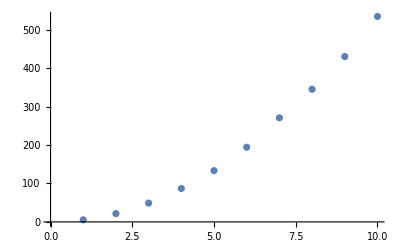

```mathematica
ListPlot[meandata[[;;,2]]]
```

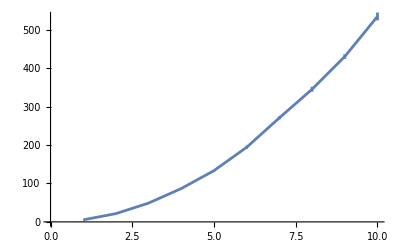

```mathematica
ErrorListPlot[meandata[[;;,2;;3]],Joined->True]
```

```mathematica
Export["/Users/snigdha/Documents/Work/Courses_IISER/PHY206-Physics_through_Computational_Thinking/mydata.csv",data]
```

/Users/snigdha/Documents/Work/Courses_IISER/PHY206-Physics_through_Computational_Thinking/mydata.csv

```mathematica
data1=Import["/Users/snigdha/Documents/Work/Courses_IISER/PHY206-Physics_through_Computational_Thinking/mydata.csv"]//TableForm
```

1 | 5.39 | 5.36 | 5.62 | 4.9 | 5.32 | 5.56 | 5.44 | 5.42 | 5.24 | 5.41
2 | 23.02 | 20.93 | 21.11 | 21.78 | 20.36 | 23.38 | 20.96 | 19.93 | 22.24 | 21.91
3 | 52.83 | 48.78 | 48.81 | 48.71 | 45.92 | 48.37 | 45.1 | 50.1 | 51.94 | 49.47
4 | 83.3 | 79.46 | 90.92 | 87.12 | 85.11 | 90.02 | 82.02 | 93.56 | 92.44 | 85.27
5 | 129.02 | 136.34 | 128.57 | 131.18 | 124.23 | 145.23 | 134. | 135.18 | 129.49 | 141.62
6 | 208.29 | 202.54 | 189.53 | 207.17 | 180.25 | 176.43 | 192.61 | 192.37 | 211.12 | 183.36
7 | 274.25 | 271.71 | 260.62 | 267.91 | 281.89 | 273.15 | 243.45 | 272.09 | 285.81 | 278.8
8 | 341.13 | 315.31 | 348.71 | 345.13 | 370.15 | 374.5 | 348.77 | 358.44 | 334.43 | 318.1
9 | 431.77 | 452.56 | 421.56 | 403.25 | 413.42 | 439.99 | 414.08 | 461.63 | 435.63 | 431.58
10 | 496.77 | 497.77 | 568.56 | 540.9 | 522.82 | 575.54 | 554.84 | 495.27 | 558.67 | 538.19

```mathematica
Manipulate[Show[Plot[a x^2,{x,1,10},PlotLabel->a],ErrorListPlot[meandata[[;;,2;;3]]]],{a,1,10}]
```

```mathematica
testfunc=Table[5 x^2,{x,1,10}]
```

{5,20,45,80,125,180,245,320,405,500}

```mathematica
(meandata[[1,2]]-testfunc[[1]])^2/meandata[[1,3]]^2
```

31.1579

```mathematica
temparray = ((meandata[[;;,2]]-testfunc)^2/meandata[[;;,3]]^2)
```

{31.1579,17.7506,25.9562,19.5052,15.9182,12.1341,42.2788,15.267,17.8676,11.8477}

```mathematica
chisq = Total[temparray]
```

209.683

```mathematica
chisqdata= Table[
f[x_]=a x^2;
chisq= Total[(meandata[[;;,2]]-Table[f[t],{t,1,10}])^2/meandata[[;;,3]]^2];
{a,chisq},{a,4,6,0.01}];
```

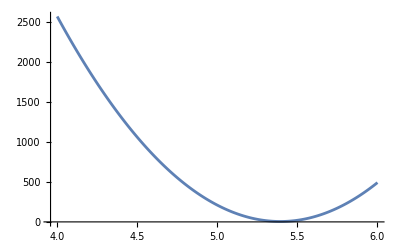

```mathematica
ListPlot[chisqdata,Joined->True]
```

```mathematica
funcfit[x_]=Fit[meandata[[;;,2]],{x^2},x]
```

5.36899 x^2

```mathematica
funcfit1[x_]=Fit[meandata[[;;,2]],{1,x,x^2},x]
```

-3.0108+1.99954 x+5.17598 x^2

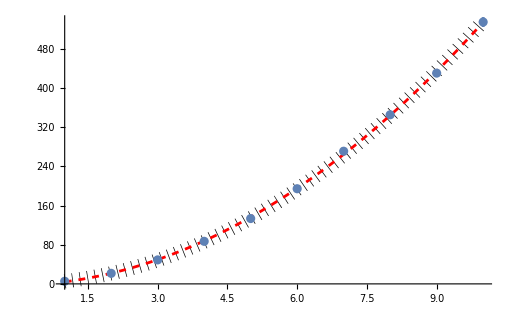

```mathematica
Show[Plot[funcfit[x],{x,1,10},PlotStyle->{Black,Dotted,Thickness[0.02]}],Plot[funcfit1[x],{x,1,10},PlotStyle->{Red,Dashed}],ErrorListPlot[meandata[[;;,2;;3]]]]
```

```mathematica
percenterror = (5.3-9.8/2)/9.8*100
```

4.08163

```mathematica
Polynomial Regression
```

```mathematica
fn[x_] = a1 + b1 x+ c1  x^2
```

a1+b1 x+c1 x^2

```mathematica
fit= FindFit[meandata[[;;,2]],{a1+b1 x+c1  x^2},{a1,b1,c1},{x}]
```

{a1→-3.0108,b1→1.99954,c1→5.17598}

--------------------Fitting exercise for class-------

```mathematica
data = Transpose[Prepend[Table[Table[Round[ -3 i^2+i^3(RandomReal[]),0.01],{i,1,10}],{10}],Range[1,10]]];
data//TableForm
```

1 | -2.61 | -2.38 | -2.75 | -2.96 | -2.32 | -2.27 | -2.72 | -2.4 | -2.3 | -2.72
2 | -8.45 | -4.9 | -9.91 | -8.51 | -8.66 | -6.04 | -4.73 | -5.02 | -8.78 | -10.83
3 | -17.93 | -11.98 | -23.88 | -17.99 | -16.76 | -14.81 | -14.22 | -10.91 | -19.66 | -15.1
4 | -16.71 | 7.59 | -47.78 | -30.64 | -14.02 | -33.01 | -10.04 | -7.22 | -4. | -10.19
5 | -50.41 | 29.23 | 13.49 | 21.72 | -52.24 | -49.74 | -64.1 | 39.55 | -47.97 | 8.32
6 | -88.49 | -25.84 | -106.39 | 89.55 | -15.89 | 9.67 | -19.08 | 47.54 | 13.64 | -68.62
7 | -9.69 | -102.83 | 158.66 | 73.57 | 64.87 | -46.49 | -69.18 | 105.14 | 55.55 | 123.01
8 | 209.45 | 200.16 | 196.32 | 214.67 | 134.92 | 37.32 | 160.9 | 21.66 | -60.22 | -31.12
9 | 398.91 | 358.1 | 341.74 | 165.72 | 322.73 | 121.89 | 161.53 | 236.59 | 460.78 | 244.4
10 | 638.01 | 209.33 | 399.47 | 148.26 | 37.48 | -170.12 | 353.95 | 76.98 | 542.11 | 238.09

```mathematica
meandata = Table[
set = data[[n,2;;]];
err = StandardDeviation[set]/Sqrt[Length[set]-1];
{n,Mean[set],err},{n,1,10}]
```

{{1,-2.543,0.079676},{2,-7.583,0.740784},{3,-16.324,1.26767},{4,-16.602,5.39924},{5,-15.215,13.5996},{6,-16.391,20.1887},{7,35.261,29.2387},{8,108.406,35.4144},{9,281.239,37.4806},{10,247.356,81.0963}}

```mathematica
meandata//TableForm
```

1 | -2.543 | 0.079676
2 | -7.583 | 0.740784
3 | -16.324 | 1.26767
4 | -16.602 | 5.39924
5 | -15.215 | 13.5996
6 | -16.391 | 20.1887
7 | 35.261 | 29.2387
8 | 108.406 | 35.4144
9 | 281.239 | 37.4806
10 | 247.356 | 81.0963

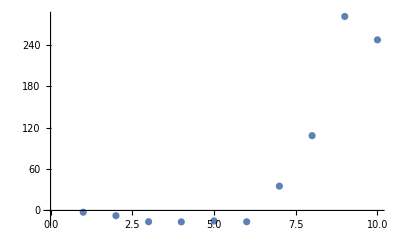

```mathematica
ListPlot[meandata[[;;,2]]]
```

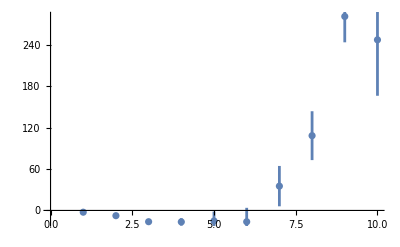

```mathematica
ErrorListPlot[meandata[[;;,2;;3]]]
```

```mathematica
funcfit1[x_]=Fit[meandata[[;;,2]],{x^2,x^3},x]
```

-3.6357 x^2+0.665092 x^3

```mathematica
fn[x_] = -3 x^2+ a1  x^3
```

-3 x^2+a1 x^3

```mathematica
fit= FindFit[meandata[[;;,2]],{ -3 x^2+a1 x^3},{a1},{x}]
```

{a1→0.594137}

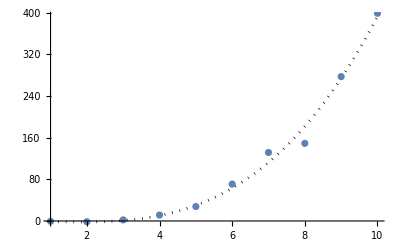

```mathematica
Show[Plot[funcfit1[x],{x,1,10},PlotStyle->{Black,Dotted}],ListPlot[meandata[[;;,2]]]]
```

```mathematica
chisqdata= Table[
f[x_]=-3 x^2+ a  x^3;
chisq= Total[(meandata[[;;,2]]-Table[f[t],{t,1,10}])^2/meandata[[;;,3]]^2];
{a,chisq},{a,-1,2,0.01}];
```

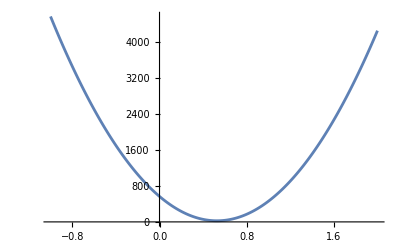

```mathematica
ListPlot[chisqdata,Joined->True]
```

```mathematica
Export["/Users/snigdha/Documents/Work/Courses_IISER/PHY206-Physics_through_Computational_Thinking/chisq.csv",meandata]
```

/Users/snigdha/Documents/Work/Courses_IISER/PHY206-Physics_through_Computational_Thinking/chisq.csv

```mathematica
datachi=Import["/Users/snigdha/Documents/Work/Courses_IISER/PHY206-Physics_through_Computational_Thinking/chisq.csv"]
```

{{1,-2.543,0.079676},{2,-7.583,0.740784},{3,-16.324,1.26767},{4,-16.602,5.39924},{5,-15.215,13.5996},{6,-16.391,20.1887},{7,35.261,29.2387},{8,108.406,35.4144},{9,281.239,37.4806},{10,247.356,81.0963}}

```mathematica
datachi//TableForm
```

1 | -2.543 | 0.079676
2 | -7.583 | 0.740784
3 | -16.324 | 1.26767
4 | -16.602 | 5.39924
5 | -15.215 | 13.5996
6 | -16.391 | 20.1887
7 | 35.261 | 29.2387
8 | 108.406 | 35.4144
9 | 281.239 | 37.4806
10 | 247.356 | 81.0963

```mathematica
ListPlot[datachi[[;;,2]]]
```

-Graphics-

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
ErrorListPlot[datachi[[;;,2;;3]]]
```

-Graphics-

```mathematica
fit= FindFit[datachi[[;;,2]],{ -3 x^2+a1 x^3},{a1},{x}]
```

{a1→0.594137}

```mathematica
chisqdata= Table[
f[x_]=-3 x^2+ a  x^3;
chisq= Total[(datachi[[;;,2]]-Table[f[t],{t,1,10}])^2/datachi[[;;,3]]^2];
{a,chisq},{a,-1,2,0.01}];
```

```mathematica
ListPlot[chisqdata,Joined->True]
```

-Graphics-